# 4Body Level Spacing Analysis

```mathematica
PBrody[x_,w_]:=(1+w)(Gamma[(2+w)/(1+w)])^(1+w)x^w Exp[-(Gamma[(2+w)/(1+w)]x)^(1+w)];
```

```mathematica
bins=Table[x,{x,0,5,0.2}];
bFit=Table[0.5*(bins[[i]]+bins[[i+1]]),{i,1,Length[bins]-1}];
```

Make a module to do everything above and output what we want

```mathematica
Analyze[MyPath_,Ewindowsize_,bins_,bFit_]:=Module[{rundata0,DD,curvestemp0,Curves0,Evals0,Ecutoff0,eValsBound0,Es0,eTrim0,avg0,ρ0,EspaceBin0,NormBrodyBinCs0,Brodyw,BrodyError,brodyPdist0,pfit0,pbrody,w,SampleRange,BrodyDistribution,x,phist0,NumSpacings,pcurves0,penergies0,pcurvesenergies,DeepStatesRange,eValsDeep0,pdeepstates0},
BrodyDistribution=ProbabilityDistribution[PBrody[x,w],{x,0,∞},Assumptions->w>0];
rundata0=Import[StringJoin[MyPath,"4BodySVD.par"],"list"];
DD=Interpreter["Number"][StringReplace[StringSplit[rundata0[[8]]],"d"->""]][[1]];

curvestemp0=Transpose[Import[StringJoin[MyPath,"AdiabaticCurves.dat"]]];
Curves0=Table[Table[{curvestemp0[[1,i]],curvestemp0[[j,i]]},{i,1,Length[curvestemp0[[1]]]}],{j,2,Length[curvestemp0]}];
Evals0=Flatten[Import[StringJoin[MyPath,"Eigenvals.dat"]]];
Ecutoff0=Evals0[[4]];
SampleRange=Ecutoff0-Ewindowsize<#<Ecutoff0-1.&;
DeepStatesRange=#<Ecutoff0-Ewindowsize&;
Evals0=Sort[Drop[Evals0,1;;4]];
eValsBound0 = Sort[Select[Evals0,SampleRange]];
eValsDeep0=Sort[Select[Evals0,DeepStatesRange]];
pcurves0=ListPlot[Curves0,FrameLabel->{"R","Energy"},PlotTheme->"Scientific",PlotStyle->{Thickness[0.005]},PlotMarkers->None,Joined->True,PlotRange->{1.05Min[curvestemp0[[2]]],Ecutoff0+40}];
penergies0=ListPlot[Table[{8,eValsBound0[[i]]},{i,1,Length[eValsBound0]}],PlotMarkers->Graphics[{Thickness[.001],Black,Line[{{1.5,0},{2,0}}]}]];
pdeepstates0=ListPlot[Table[{8,eValsDeep0[[i]]},{i,1,Length[eValsDeep0]}],PlotMarkers->Graphics[{Thickness[.001],Red,Line[{{1.5,0},{2,0}}]}]];
pcurvesenergies=Show[pcurves0,penergies0,pdeepstates0,Frame->True];
Es0=Table[eValsBound0[[i+1]]-eValsBound0[[i]],{i,1,Length[eValsBound0]-1}];
eTrim0= Select[Es0,#>0.000001&];
NumSpacings=Length[eTrim0];
avg0 = Mean[eTrim0];
eTrim0 = eTrim0/avg0;
ρ0=1/avg0;
EspaceBin0=BinCounts[eTrim0,{bins}];
NormBrodyBinCs0=Table[EspaceBin0[[i]]/Total[EspaceBin0]/(bins[[i+1]]-bins[[i]]),{i,1,Length[bins]-1}];
Brodyw=w/.FindDistributionParameters[eTrim0,BrodyDistribution];
BrodyError=√(-1/D[LogLikelihood[BrodyDistribution,eTrim0],{w,2}])/.w->Brodyw;
brodyPdist0 = Table[{bFit[[i]],NormBrodyBinCs0[[i]]},{i,1,Length[bFit]}];
phist0=ListPlot[brodyPdist0,InterpolationOrder->0,Joined->True,PlotRange->All,PlotStyle->Black,PlotMarkers->None];
(*pars0 = FindFit[brodyPdist0,{PBrody[s,w],w>0,w<1},{w},s]*)
pfit0=Plot[PBrody[s,Brodyw],{s,0,5},PlotRange->All,PlotStyle->Red];
pbrody=Show[phist0,pfit0,FrameLabel->{"s / s̄","P(s)"},Frame-> True,LabelStyle->Medium,Epilog->{Text[Style["w = ",Medium],{2.5,0.6}],Text[Style[DecimalForm[Brodyw,{2,2}]±DecimalForm[BrodyError,{2,2}],Medium],{3.9,0.6}]}];
{DD,NumSpacings,ρ0,Brodyw,BrodyError,pcurvesenergies,pbrody}

]
```

```mathematica
Ewindowsize=10.0;
```

```mathematica
Type1Paths={"/Users/niravmehta/Documents/GitHub/4BodySVD/runs20/run1/",
"/Users/niravmehta/Documents/GitHub/4BodySVD/runs30/run1/",
"/Users/niravmehta/Documents/GitHub/4BodySVD/runs40/run1/",
"/Users/niravmehta/Documents/GitHub/4BodySVD/runs50/run1/",
"/Users/niravmehta/Documents/GitHub/4BodySVD/runs75/run1/"};
Type2Paths={"/Users/niravmehta/Documents/GitHub/4BodySVD/runs20/run2/",
"/Users/niravmehta/Documents/GitHub/4BodySVD/runs30/run2/",
"/Users/niravmehta/Documents/GitHub/4BodySVD/runs40/run2/",
"/Users/niravmehta/Documents/GitHub/4BodySVD/runs50/run2/",
"/Users/niravmehta/Documents/GitHub/4BodySVD/runs75/run2/"};
Type3Paths={"/Users/niravmehta/Documents/GitHub/4BodySVD/runs20/run3/",
"/Users/niravmehta/Documents/GitHub/4BodySVD/runs30/run3/",
"/Users/niravmehta/Documents/GitHub/4BodySVD/runs40/run3/",
"/Users/niravmehta/Documents/GitHub/4BodySVD/runs50/run3/",
"/Users/niravmehta/Documents/GitHub/4BodySVD/runs75/run3/"};
Type4Paths={"/Users/niravmehta/Documents/GitHub/4BodySVD/runs20/run4/",
"/Users/niravmehta/Documents/GitHub/4BodySVD/runs30/run4/",
"/Users/niravmehta/Documents/GitHub/4BodySVD/runs40/run4/",
"/Users/niravmehta/Documents/GitHub/4BodySVD/runs50/run4/",
"/Users/niravmehta/Documents/GitHub/4BodySVD/runs75/run4/"};
```

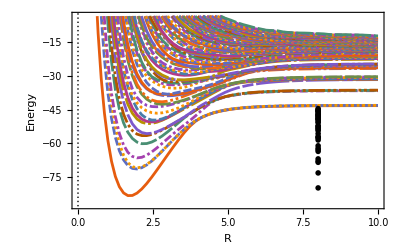
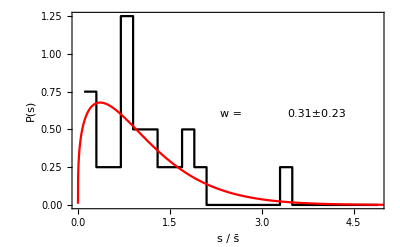
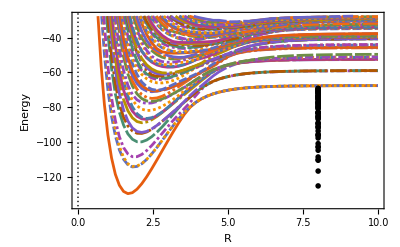
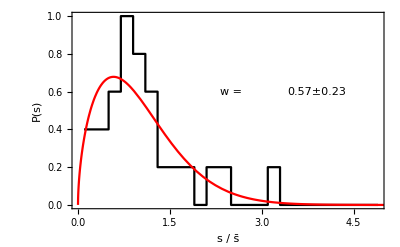
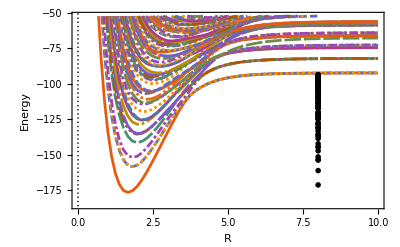
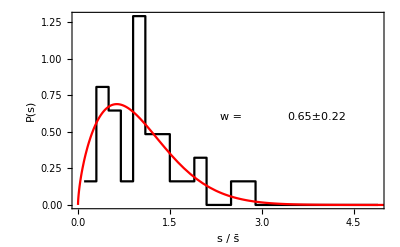
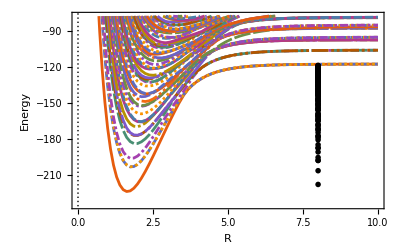
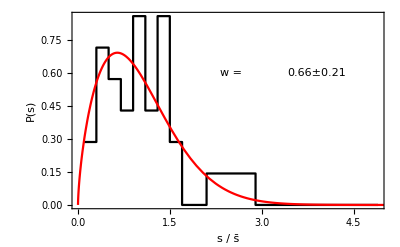
{{20.,20,2.35813,0.311203,0.230628,-Graphics-,-Graphics-},{30.,25,3.00089,0.56529,0.227226,-Graphics-,-Graphics-},{40.,31,3.6676,0.647363,0.224183,-Graphics-,-Graphics-},{50.,35,3.93073,0.660626,0.208086,-Graphics-,-Graphics-},{75.,42,4.74776,0.517895,0.186138,-Graphics-,-Graphics-}}

```mathematica
Type1Data=Table[Analyze[Type1Paths[[i]],Ewindowsize,bins,bFit],{i,1,Length[Type1Paths]}]
```

```mathematica
rhodat1=Table[{√Type1Data[[i,1]],Type1Data[[i,3]]},{i,1,Length[Type1Data]}]
```

{{4.47214,2.35813},{5.47723,3.00089},{6.32456,3.6676},{7.07107,3.93073},{8.66025,4.74776}}

```mathematica
QMdosline=Fit[rhodat1,{1,x},x]
```

-0.0965947+0.568284 x

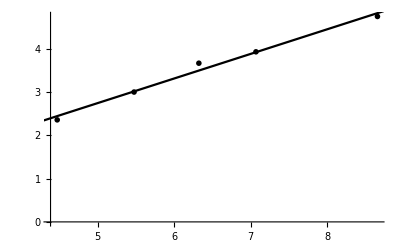

```mathematica
Show[ListPlot[rhodat1],Plot[QMdosline,{x,0,√100}]]
```